```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v3

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,870,960,10}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,870,960,10}];
r422=chi4/chi2;
r422[[1]]=r422[[1]][[17;;-1]];
```

```mathematica
mub=Table[i,{i,870,960,10}];
T=Table[i,{i,17,120,1}];
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r422[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
Export["r42high.dat",R42all]
```

r42high.dat

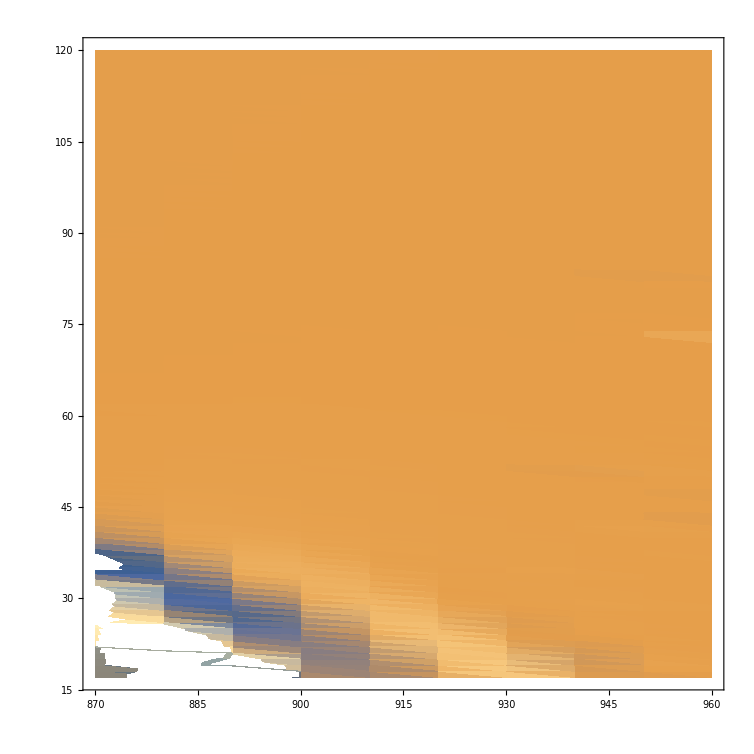

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-5,5}}]
```

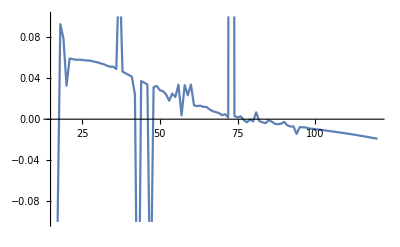

```mathematica
ListLinePlot[{Transpose[{T,r422[[10]]}]},PlotRange->{All,{-0.1,0.1}}]
```